```mathematica
(* Notebook for the scattering of a massive particle off a finite cylindrical barrier *)
```

```mathematica
(* First define useful functions pertaining to the combination of Bessel and Neumann functions, and similarly for their derivatives. *)
ClearAll;
SubMinus[χ][m_,k_,a_]:=(BesselJ[m,k*a]-ⅈ*BesselY[m,k*a]);
SubPlus[χ][m_,k_,a_]:=(BesselJ[m,k*a]+ⅈ*BesselY[m,k*a]);
JPRIME[m_,k_,a_]:=1/2(BesselJ[m-1,k*a]-BesselJ[m+1,k*a]);
YPRIME[m_,k_,a_]:=1/2(BesselY[m-1,k*a]-BesselY[m+1,k*a]);
SubMinus[ξ][m_,k_,a_]:=(JPRIME[m,k,a]-ⅈ*YPRIME[m,k,a]);
SubPlus[ξ][m_,k_,a_]:=(JPRIME[m,k,a]+ⅈ*YPRIME[m,k,a]);
β[m_,k_,a_]:=a*k*JPRIME[m,k,a]/BesselJ[m,k*a];
```

```mathematica
(* Define the phase shift function δ(m,k,a) using the expression found in [Two-Dimensional time-dependent quantum-mechanical scattering event - I. Galbraith, Y. Sing Ching, E. Abraham, Am. J. Phys. vol. 52, pp. 60-68, Jan 1984]. Note that the quantity δ(m,k,a) actually corresponds to exp(2 Subscript[ⅈδ, m]) *)
δ[m_,k_,a_]:=(-SubMinus[χ][m,k,a])/(SubPlus[χ][m,k,a])*(1+k*a*((SubPlus[ξ][m,k,a])/(SubPlus[χ][m,k,a])-(SubMinus[ξ][m,k,a])/(SubMinus[χ][m,k,a]))(β[m,k,a]-k*a*(SubPlus[ξ][m,k,a])/(SubPlus[χ][m,k,a]))^-1);
```

```mathematica
(* Apply the equation for the scattering amplitude and take the square of the absolute value. *)
f[n_,k_,a_,ϕ_]:=Abs[Sqrt[1/(2*π*ⅈ*90)]*((δ[0,k,a]-1)+Sum[2*Cos[m*ϕ]*(δ[m,k,a]-1),{m,1,n}])]^2;
```

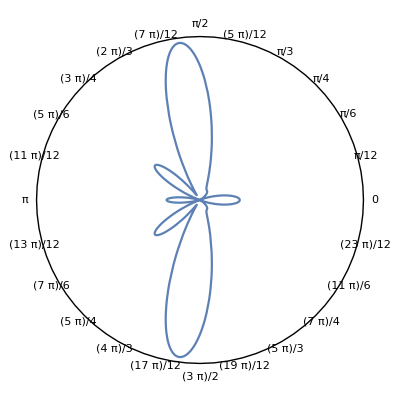

```mathematica
(* Plot the results *)
PolarPlot[f[5,45,0.09,ϕ],{ϕ,0,2*π}, PolarAxes->Automatic, PlotRange->All]
```